```mathematica
PPKTP Quasi Phasematching
```

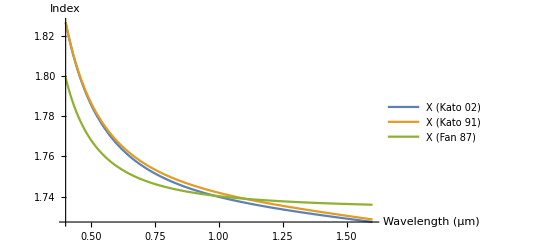

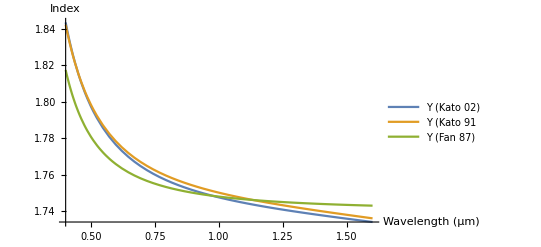

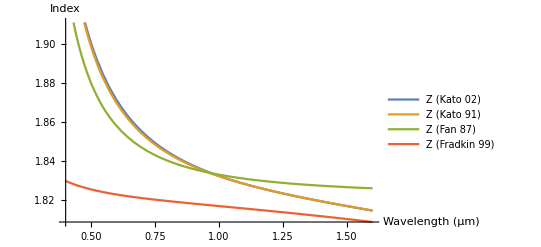

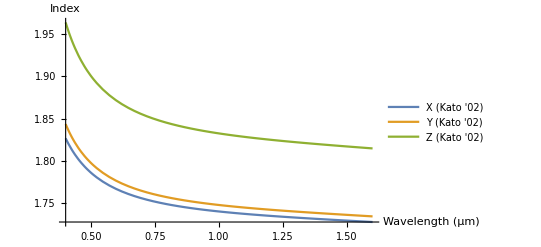

```mathematica
(* Note: there are a lot of Sellmeier-type equations in the literature for PPKTP.
It's not at all obvious which are most accurate, so I've collected as many as possible here and more or less tried them all.*)

(* These are from Kato and Takaoka 2002 *)
xindexkato02[λ_]:=√(3.29100+0.04140/(λ^2-0.03978)+9.35522/(λ^2-31.45571));
yindexkato02[λ_]:=√(3.45018+0.04341/(λ^2-0.04597)+16.98825/(λ^2-39.43799));
zindexkato02[λ_]:=√(4.59423+0.06206/(λ^2-0.04763)+110.80672/(λ^2-86.12171));

(* These are from Kato 1991, for flux-grown KTP, with the blessing of Dmitriev et al *)
xindexkato91[λ_]:=√(3.0065+0.03901/(λ^2-0.04251)-0.01327 λ^2);
yindexkato91[λ_]:=√(3.0333+0.04154/(λ^2-0.04547)-0.01408 λ^2);
zindexkato91[λ_]:=√(3.3134+0.05694/(λ^2-0.05658)-0.01682 λ^2);

(* These are from Fan et al 1987 *)
(* Note: Raicol claim they use these, plus Fradkin's correction below. *)
xindexfan87[λ_]:=√(2.16747+0.83733/(1-0.04611/λ^2) -0.01713/λ^2);
yindexfan87[λ_]:=√(2.19229+0.83547/(1-0.04970/λ^2) -0.01621/λ^2);
zindexfan87[λ_]:=√(2.25411+1.06543/(1-0.05486/λ^2) -0.02140/λ^2);

(* The Z refractive index correction from Fradkin 1999 *)
(* Note: Raicol claim to use this. *)
zindexfradkin99[λ_]:=√(2.12725+1.18431/(1-0.00514852/λ^2) + 0.6603/(1-100.00507/λ^2)-0.00968956 λ^2);

(* Visualize the indices. *)
Plot[
{xindexkato02[λ],
xindexkato91[λ],
xindexfan87[λ]},
{λ,0.4,1.6},
PlotLegends -> {"X (Kato 02)",
"X (Kato 91)",
"X (Fan 87)"},
AxesLabel -> {"Wavelength (μm)", "Index"}]

Plot[
{yindexkato02[λ],
yindexkato91[λ],
yindexfan87[λ]},
{λ,0.4,1.6},
PlotLegends -> { "Y (Kato 02)",
 "Y (Kato 91",
 "Y (Fan 87)"},
AxesLabel -> {"Wavelength (μm)", "Index"}]

Plot[
{zindexkato02[λ],zindexkato91[λ],zindexfan87[λ],zindexfradkin99[λ]},
{λ,0.4,1.6},
PlotLegends -> {"Z (Kato 02)","Z (Kato 91)", "Z (Fan 87)", "Z (Fradkin 99)"},
AxesLabel -> {"Wavelength (μm)", "Index"}]

(* Selecting indices for later calculations. Looks like Kato 2002 works best. *)
xindex[λ_] := xindexkato02[λ];
yindex[λ_] := yindexkato02[λ];
zindex[λ_] := zindexkato02[λ];

Plot[
{xindexkato02[λ],yindexkato02[λ],zindexkato02[λ]},{λ,0.4,1.6},
AxesLabel->{"Wavelength (μm)","Index"},
PlotLegends->{"X (Kato '02)","Y (Kato '02)", "Z (Kato '02)"}
]
```

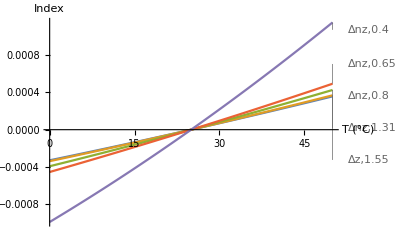

```mathematica
(* Coefficient of thermal expansion, from Emanueli & Arie 2003 *)
α=6.7*10^-6;
β=11*10^-9;
cte[t_] := 1+α(t-25)+β(t-25);

(* Temperature dependence of the index from Emanueli & Arie 2003 *)
nz1={a0->9.9587*10^-6, a1->9.9228*10^-6,a2-> -8.9603*10^-6,a3-> 4.1010*10^-6};
nz2={a0->-1.1882*10^-8, a1->10.459*10^-8, a2-> -9.8136*10^-8, a3-> 3.1481*10^-8};
ny1={a0->6.2897*10^-6, a1->6.3061*10^-6, a2->-6.0629*10^-6, a3-> 2.6486*10^-6};
ny2={a0->-0.14445*10^-8,a1->2.2244*10^-8, a2->-3.5770*10^-8, a3->1.3470*10^-8};
n12[λ_,axis_,order_] :=( a0+a1/λ+a2/λ^2+a3/λ^3)/.(
If[axis=="z" &&order==1, nz1,
If[axis=="z"&& order==2,nz2,
If[axis=="y" &&order==1, ny1,
If[axis=="y" && order==2, ny2, 0]]]]);
dnzemanueli03[λ_,t_] :=n12[λ,"z",1]*(t-25)+n12[λ,"z",2]*(t-25)^2;
dnyemanueli03[λ_,t_] :=n12[λ,"y",1]*(t-25)+n12[λ,"y",2]*(t-25)^2;

(* And these are from Kato 1992, with the blessing of Dmitriev et al *)

dnxkato92[λ_,t_]:=(0.1323/λ^3-0.4385/λ^2+1.2307/λ+0.7709)*10^-5*(t-20);
dnykato92[λ_,t_]:=(0.5014/λ^3-2.0030/λ^2+3.3016/λ+0.7498)*10^-5*(t-20);
dnzkato92[λ_,t_]:=(0.3896/λ^3-1.3332/λ^2+2.2762/λ+2.1151)*10^-5*(t-20);

(* Found more from the Kato 2002 paper! *)
(* dnx and dny between 0.43um and 1.58um *)
dnxkato02[λ_,t_]:=(0.1717/λ^3+0.5353/λ^2+0.8416/λ+0.1627)*10^-5*(t-20);
dnykato02[λ_,t_]:=(0.1997/λ^3+0.4063/λ^2+0.5154/λ+0.5425)*10^-5*(t-20);
(* dnz between 0.53um and 1.57um *)
dnzkato02[λ_,t_]:=(0.9221/λ^3+2.9220/λ^2+3.6677/λ+0.1897)*10^-5*(t-20);

(* Here is where I pick which of the curves to use. *)
dnx[λ_,t_]:=dnxkato02[λ,t];
dny[λ_,t_]:=dnyemanueli03[λ,t];
dnz[λ_,t_]:=dnzemanueli03[λ,t];

(* The point of this plot is to look at whether the temperature makes a bigger difference in the visible sources. *)
(* Spoiler: yes, it does. *)
Plot[
{dnz[1.55,t],dnz[1.31,t],dnz[0.8,t],dnz[0.65,t],dnz[0.4,t]},
{t,0,50},
PlotLabels->{"Δz,1.55","Δnz,1.31", "Δnz,0.8","Δnz,0.65","Δnz,0.4"},
AxesLabel->{"T (°C)","Index"}]
```

```mathematica
(* Other helper functions *)

(* find the complementary idler/signal given a pump wavelength *)
sister[λ_, λp_] := (1/λp-1/λ)^-1;

(* Delta K for type 0 and type 2. *)
Δktype0[λp_,λs_,λi_,t_] := 2*Pi*((zindex[λp]+dnz[λp,t])/λp-(zindex[λs]+dnz[λs,t])/λs-(zindex[λi]+dnz[λi,t])/λi);
Δktype2[λp_,λs_,λi_,t_]:= 2*Pi*((yindex[λp]+dny[λp,t])/λp-(yindex[λs]+dny[λs,t])/λs-(zindex[λi]+dnz[λi,t])/λi);

(* Emission intensity is a function of delta-k, and crystal length, easy to define these here. *)
intensitytype0[λp_,λs_,λi_,t_,Λ_,L_]:=
Sinc[(Δktype0[λp,λs,λi,t]-2*Pi/(Λ*cte[t]))*(L*cte[t])/2]^2;
intensitytype2[λp_,λs_,λi_,t_,Λ_,L_]:=
Sinc[(Δktype2[λp,λs,λi,t]+2*Pi/(Λ*cte[t]))*(L*cte[t])/2]^2;
```

```mathematica
(* Temperature tuning behaviour, quick example (seen in the lab). *)
Module[{Λ,λ,λp,t,L},
Λ = 52.8; (* Poling period in microns. Raicol specify 54.05 but we get better predictions using 52.8: this we take to be the result of imperfect Sellmeier coefficients, particularly in this wavelength range. *);
λp = 0.658; (* Pump wavelength *)
L=10000;
ListDensityPlot[
Table[Evaluate[intensitytype2[λp,λ,sister[λ,λp],t,Λ,L]+intensitytype2[λp,sister[λ,λp],λ,t,Λ,L]],
{λ,1.305,1.33,0.0001},
{t,-150,170,2}
],
DataRange->{{-150,170},{1305,1330}},
PlotRange->Full,
ImageSize->{640,380},
AspectRatio->3/6,
PlotLegends->Automatic,
FrameLabel->{"T (°C)","Wavelength (nm)"}
]
]
```

-Graphics-

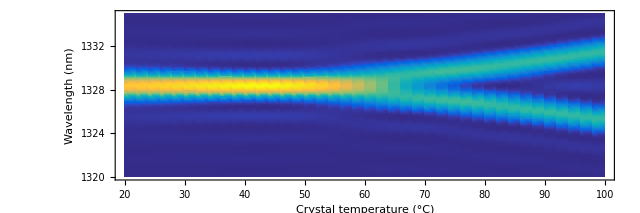

```mathematica
(* Plots for the publication are below. *)

parulaOld=Blend[{{0,RGBColor[0.2081,0.1663,0.5292]},{8/255,RGBColor[0.2123,0.2132,0.6258]},{13/255,RGBColor[0.2063,0.244,0.6878]},{1/15,RGBColor[0.1921,0.2698,0.7381]},{19/255,RGBColor[0.1802,0.2832,0.7634]},{22/255,RGBColor[0.1541,0.3052,0.8017]},{8/85,RGBColor[0.1295,0.3217,0.8269]},{5/51,RGBColor[0.1147,0.3306,0.8387]},{26/255,RGBColor[0.0986,0.3397,0.8495]},{28/255,RGBColor[0.0646,0.3572,0.8664]},{2/17,RGBColor[0.0329,0.3724,0.8765]},{31/255,RGBColor[0.0213,0.3792,0.8796]},{11/85,RGBColor[0.0086,0.3911,0.8827]},{12/85,RGBColor[0.0054,0.4066,0.8831]},{38/255,RGBColor[0.0089,0.4159,0.8816]},{44/255,RGBColor[0.0306,0.441,0.8729]},{1/5,RGBColor[0.0582,0.4677,0.8589]},{61/255,RGBColor[0.0782,0.5051,0.8378]},{67/255,RGBColor[0.0778,0.5295,0.828]},{24/85,RGBColor[0.0668,0.5527,0.8243]},{26/85,RGBColor[0.0445,0.5826,0.8223]},{27/85,RGBColor[0.0342,0.5968,0.8198]},{28/85,RGBColor[0.0279,0.6097,0.8154]},{29/85,RGBColor[0.0248,0.6214,0.8091]},{92/255,RGBColor[0.0233,0.6384,0.7948]},{32/85,RGBColor[0.0227,0.6503,0.781]},{101/255,RGBColor[0.0263,0.6637,0.7615]},{104/255,RGBColor[0.0338,0.6712,0.749]},{109/255,RGBColor[0.0574,0.6831,0.7267]},{112/255,RGBColor[0.0755,0.6899,0.7126]},{116/255,RGBColor[0.1031,0.6986,0.6929]},{118/255,RGBColor[0.118,0.7028,0.6827]},{121/255,RGBColor[0.1418,0.7089,0.6669]},{124/255,RGBColor[0.1671,0.7148,0.6507]},{128/255,RGBColor[0.2033,0.7223,0.6281]},{131/255,RGBColor[0.2324,0.7275,0.6107]},{133/255,RGBColor[0.2527,0.7308,0.5988]},{8/15,RGBColor[0.2845,0.7354,0.5809]},{139/255,RGBColor[0.3177,0.7394,0.563]},{47/85,RGBColor[0.3405,0.7417,0.5512]},{48/85,RGBColor[0.3753,0.7446,0.5339]},{146/255,RGBColor[0.3986,0.7461,0.5229]},{148/255,RGBColor[0.4218,0.7473,0.5123]},{151/255,RGBColor[0.4561,0.7485,0.4972]},{31/51,RGBColor[0.5,0.7491,0.4786]},{53/85,RGBColor[0.5418,0.749,0.4613]},{163/255,RGBColor[0.5816,0.7482,0.4451]},{167/255,RGBColor[0.6197,0.7469,0.4298]},{173/255,RGBColor[0.6742,0.7441,0.4081]},{59/85,RGBColor[0.7091,0.7418,0.3942]},{63/85,RGBColor[0.8085,0.7336,0.3539]},{196/255,RGBColor[0.8642,0.7288,0.33]},{202/255,RGBColor[0.911,0.7259,0.3078]},{206/255,RGBColor[0.9417,0.7259,0.2907]},{208/255,RGBColor[0.9567,0.7273,0.2808]},{14/17,RGBColor[0.9708,0.7303,0.2696]},{212/255,RGBColor[0.9831,0.7355,0.257]},{214/255,RGBColor[0.9922,0.7431,0.2437]},{43/51,RGBColor[0.9952,0.7476,0.2373]},{217/255,RGBColor[0.9986,0.7573,0.2251]},{44/51,RGBColor[0.9985,0.7726,0.209]},{74/85,RGBColor[0.9964,0.7829,0.1995]},{15/17,RGBColor[0.9914,0.7981,0.1863]},{76/85,RGBColor[0.9851,0.8133,0.174]},{236/255,RGBColor[0.9672,0.8548,0.1425]},{16/17,RGBColor[0.9611,0.8774,0.1258]},{81/85,RGBColor[0.9588,0.8958,0.1126]},{247/255,RGBColor[0.9599,0.9225,0.0944]},{50/51,RGBColor[0.9641,0.9443,0.0802]},{1,RGBColor[0.9763,0.9831,0.0538]}},#1]&;

(* This is the same as the plot above, but reformatted for publication. *)
Module[{Λ,λ,λp,t,L},
Λ = 52.8; (* Poling period in microns. Raicol specify 54.05 but we get better predictions using 52.8? *);
L=10000;

λp = 0.6642; (* Pump 664nm *)
ListDensityPlot[
Table[Evaluate[intensitytype2[λp,λ,sister[λ,λp],t,Λ,L]+intensitytype2[λp,sister[λ,λp],λ,t,Λ,L]],
{λ,1.320,1.335,0.0001},
{t,20,100,2}
],
DataRange->{{20,100},{1320,1335}},
PlotRange->Full,
ImageSize->{640,380},
AspectRatio->2/6,
PlotLegends->Automatic,
ColorFunction->parulaOld,
PlotRangePadding->0,
FrameLabel->{"Crystal temperature (°C)","Wavelength (nm)"}
]
]
```

```mathematica
Phase compensation for prototype entangled source
```

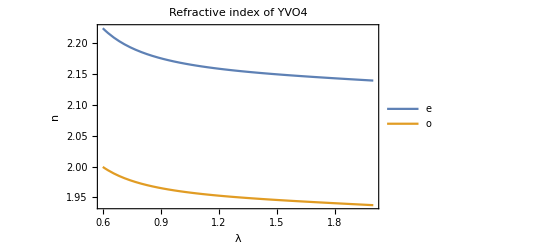

```mathematica
(* Refractive index of YVO4 post-compensation crystals. *)
ordyvo = {a1-> 3.77834, a2-> 0.069736, a3-> 0.04724, a4-> 0.0108133};
extyvo = {a1-> 4.59905, a2-> 0.110534, a3-> 0.04813, a4-> 0.0122676};
nyvo[λ_, pol_] := Sqrt[a1+a2/(λ^2-a3)-a4 λ^2]/.(If[pol=="e",extyvo,ordyvo]);
Plot[
{nyvo[λ,"e"],nyvo[λ,"o"]},
{λ,0.6,2.0},
PlotLabel->"Refractive index of YVO4",
PlotLegends->{"e","o"},
AxesLabel->{"λ","n"},
Frame->True
]
```

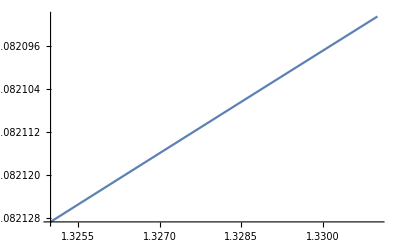

```mathematica
(* Birefringence of x-cut KTP *)
Plot[{yindex[λ]-zindex[λ]},
{λ,1.325,1.331}]
```

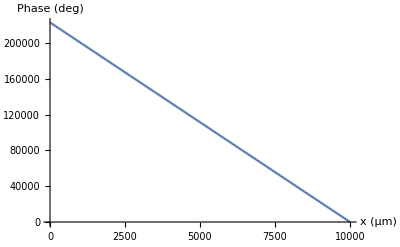

222991.

```mathematica
(* In TypeII SPDC in PPKTP, the polarizations are Y -> YZ *)

(* Both Signal and Idler are born in the same place in the crystal, but we don't know where.
 Call this location "x", in a crystal of length L. *)
signalphase[x_,L_,λs_,t_] := 2*Pi*(L-x)*(yindex[λs]+dny[λs,t])/λs;
idlerphase[x_,L_,λi_,t_] := 2*Pi*(L-x)*(zindex[λi]+dnz[λi,t])/λi;

(* Plot relative signal/idler phase at the degenerate wavelength as a function of where they originate in the cyrstal... *)
Module[{λp,λ,t,L,Λ,Lmgf,Lqtz},
λp = 0.664; (* degenerate case per previous calculations. *)
t = 50; (* degenerate case per previous calculations. *)
L = 10000;

Plot[
{(-signalphase[x,L,2λp,t]+idlerphase[x,L,2λp,t])/Pi*180},
{x,0,L},
AxesLabel->{"x (μm)","Phase (deg)"}]
]

(* This plot gives an idea of the magnitude of the phase difference between signal and idler, based on their apparent origin within the crystal. But the source we are designing uses postselection to only consider the case where signal and idler go to opposite output modes. This particular phase should just factor out. *)
```

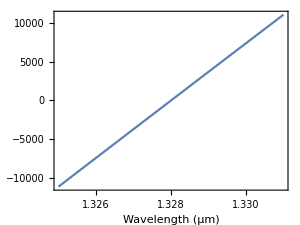

```mathematica
(* Wavelength dependence is more problematic, because it can produce a mixed state and obscure polarization correlations. Now we make the assumption that both photons are born in the centre of the crystal (x=5000) and plot the wavelength dependence of the phase. *)
Module[{λp,λ,t,L,Λ,Lmgf,Lqtz},
λp = 0.664; (* degenerate case per previous calculations. *)
t = 50; (* degenerate case per previous calculations. *)
L = 10000;
x=5000;

offset = idlerphase[x,L,2λp,t]-signalphase[x,L,2λp,t];

Plot[
{(-signalphase[x,L,λ,t]+idlerphase[x,L,sister[λ,λp],t]-offset)/Pi*180},
{λ,1.325,1.331},
FrameLabel->{"Wavelength (μm)","Relative Phase (deg)"},
Frame->True,
AspectRatio->1.5/2,
ImageSize->{300,200},
FrameStyle->Directive[Black,14]]
]
```

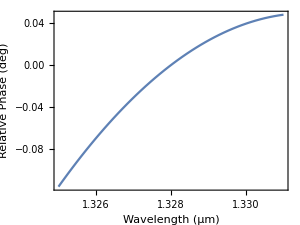

```mathematica
(* This looks like something we can compensate with a chunk of YVO4 *)
(* Assume the signal is ordinary and idler is extraordinary in the YVO4. *)
signalphasecomp[LC_,λs_] := 2*Pi*LC*(nyvo[λs,"o"]/λs);
idlerphasecomp[LC_,λi_] := 2*Pi*LC*(nyvo[λi,"e"]/λi);
Module[{λp,λ,t,L,Λ,Lmgf,Lqtz},
λp = 0.664; (* degenerate case per previous calculations. *)
t = 50; (* degenerate case per previous calculations. *)
L = 10000;
x=5000;
Lyvo4 = 4338.73;

offset = idlerphase[x,L,2λp,t]-signalphase[x,L,2λp,t];
(*  *)
Plot[
{-(idlerphasecomp[Lyvo4,sister[λ,λp]]-signalphasecomp[Lyvo4,λ]-idlerphasecomp[Lyvo4,2*λp]+signalphasecomp[Lyvo4,2*λp])/Pi*180
+(idlerphase[x,L,sister[λ,λp],t]-signalphase[x,L,λ,t]-offset)/Pi*180},
{λ,1.325,1.331},
FrameLabel->{"Wavelength (μm)","Relative Phase (deg)"},
Frame->True,
AspectRatio->1.5/2,
ImageSize->{300,200},
FrameStyle->Directive[Black,14]]
]
```

Temperature tuning maps for a range of wavelengths

44.9445

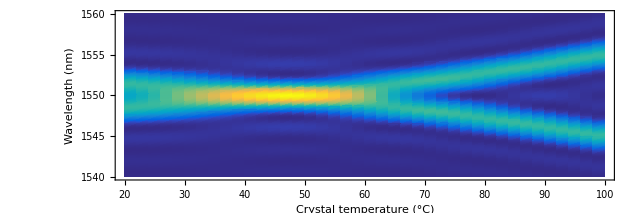

```mathematica
Module[{Λ,λ,λp,t,L},
λtarget = 1.55;
Λ= -2*Pi*cte[50]/Δktype2[λtarget/2,λtarget,λtarget,50];
Print[Λ];
L=10000;

λp = λtarget/2; (* Pump *)
ListDensityPlot[
Table[Evaluate[intensitytype2[λp,λ,sister[λ,λp],t,Λ,L]+intensitytype2[λp,sister[λ,λp],λ,t,Λ,L]],
{λ,λtarget-0.01,λtarget+0.01,0.0001},
{t,20,100,2}
],
DataRange->{{20,100},{λtarget*1000-10,λtarget*1000+10}},
PlotRange->Full,
ImageSize->{640,380},
AspectRatio->2/6,
PlotLegends->Automatic,
ColorFunction->parulaOld,
PlotRangePadding->0,
FrameLabel->{"Crystal temperature (°C)","Wavelength (nm)"}
]
]
```

54.6032

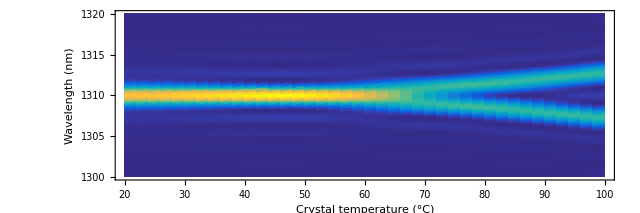

```mathematica
(* Compute generic case for 1310 *)

Module[{Λ,λ,λp,t,L},
λtarget = 1.31;
Λ= -2*Pi*cte[50]/Δktype2[λtarget/2,λtarget,λtarget,50];
Print[Λ];
L=10000;

λp = λtarget/2; (* Pump *)
ListDensityPlot[
Table[Evaluate[intensitytype2[λp,λ,sister[λ,λp],t,Λ,L]+intensitytype2[λp,sister[λ,λp],λ,t,Λ,L]],
{λ,λtarget-0.01,λtarget+0.01,0.0001},
{t,20,100,2}
],
DataRange->{{20,100},{λtarget*1000-10,λtarget*1000+10}},
PlotRange->Full,
ImageSize->{640,380},
AspectRatio->2/6,
PlotLegends->Automatic,
ColorFunction->parulaOld,
PlotRangePadding->0,
FrameLabel->{"Crystal temperature (°C)","Wavelength (nm)"}
]
]
```

-450.544

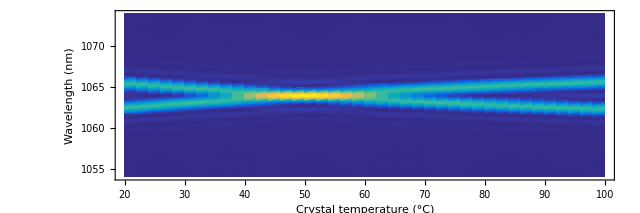

```mathematica
Module[{Λ,λ,λp,t,L},
(* Compute the period for degenerate TypeII at 1310, 50degC *)
λtarget = 1.064;
Λ= -2*Pi*cte[50]/Δktype2[λtarget/2,λtarget,λtarget,50];
Print[Λ];
L=10000;

λp = λtarget/2; (* Pump *)
ListDensityPlot[
Table[Evaluate[intensitytype2[λp,λ,sister[λ,λp],t,Λ,L]+intensitytype2[λp,sister[λ,λp],λ,t,Λ,L]],
{λ,λtarget-0.01,λtarget+0.01,0.0001},
{t,20,100,2}
],
DataRange->{{20,100},{λtarget*1000-10,λtarget*1000+10}},
PlotRange->Full,
ImageSize->{640,380},
AspectRatio->2/6,
PlotLegends->Automatic,
ColorFunction->parulaOld,
PlotRangePadding->0,
FrameLabel->{"Crystal temperature (°C)","Wavelength (nm)"}
]
]
```

```mathematica
Module[{Λ,λ,λp,t,L},
λtarget = 0.8;
Λ= -2*Pi*cte[50]/Δktype2[λtarget/2,λtarget,λtarget,50];
Print[Λ];
L=10000;

λp = λtarget/2; (* Pump *)
ListDensityPlot[
Table[Evaluate[intensitytype2[λp,λ,sister[λ,λp],t,Λ,L]+intensitytype2[λp,sister[λ,λp],λ,t,Λ,L]],
{λ,λtarget-0.01,λtarget+0.01,0.0001},
{t,20,100,0.5}
],
DataRange->{{20,100},{λtarget*1000-10,λtarget*1000+10}},
PlotRange->Full,
ImageSize->{640,380},
AspectRatio->2/6,
PlotLegends->Automatic,
ColorFunction->parulaOld,
PlotRangePadding->0,
FrameLabel->{"Crystal temperature (°C)","Wavelength (nm)"}
]
]
```

-9.26025

-Graphics-

```mathematica
-2*Pi*cte[50]/Δktype2[0.655,1.31,1.31,50]
```

54.6032

102.152

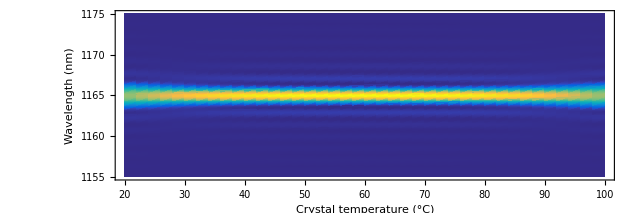

```mathematica
Module[{Λ,λ,λp,t,L},
λtarget = 1.165;
Λ= -2*Pi*cte[50]/Δktype2[λtarget/2,λtarget,λtarget,50];
Print[Λ];
L=10000;

λp = λtarget/2; (* Pump *)
ListDensityPlot[
Table[Evaluate[intensitytype2[λp,λ,sister[λ,λp],t,Λ,L]+intensitytype2[λp,sister[λ,λp],λ,t,Λ,L]],
{λ,λtarget-0.01,λtarget+0.01,0.0001},
{t,20,100,2}
],
DataRange->{{20,100},{λtarget*1000-10,λtarget*1000+10}},
PlotRange->Full,
ImageSize->{640,380},
AspectRatio->2/6,
PlotLegends->Automatic,
ColorFunction->parulaOld,
PlotRangePadding->0,
FrameLabel->{"Crystal temperature (°C)","Wavelength (nm)"}
]
]
```

```mathematica
Helping to understand the mechanism for temperature indepdence.
```

Syntax::sntxi: Incomplete expression; more input is needed .

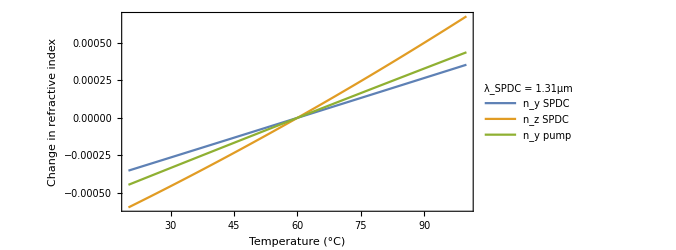

```mathematica
(* Plot the change in refractive index, with repect to the index at 60C *)
λtarget = 1.31;
dcyp = yindex[λtarget/2]+dny[λtarget/2,60];
dcy = yindex[λtarget]+dny[λtarget,60];
dcz = zindex[λtarget]+dnz[λtarget,60];
Plot[
{yindex[λtarget]+dny[λtarget,t]-dcy, zindex[λtarget]+dnz[λtarget,t]-dcz, yindex[λtarget/2]+dny[λtarget/2,t]-dcyp},
{t,20,100},
PlotLegends->LineLegend[{"n_y SPDC", "n_z SPDC", "n_y pump"},LegendLabel->"λ_SPDC = " <>ToString[λtarget]<>"μm"],
FrameLabel->{"Temperature (°C)","Change in refractive index"},
Frame->True,
AspectRatio->1/2,
ImageSize->{500,300},
FrameStyle->Directive[Black,14]]
```

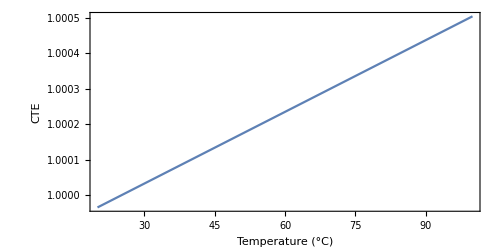

```mathematica
(* Plot the CTE of KTP over this range *)
Plot[
{cte[t]},
{t,20,100},
FrameLabel->{"Temperature (°C)","CTE"},
Frame->True,
AspectRatio->1/2,
ImageSize->{500,300},
FrameStyle->Directive[Black,14]]
```

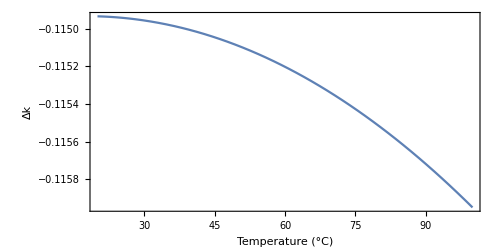

```mathematica
(* Plot the phase mismatch for degenerate SPDC over this range, for 1310 *)
Plot[
{Δktype2[0.655,1.31,1.31,t]},
{t,20,100},
FrameLabel->{"Temperature (°C)","Δk"},
Frame->True,
AspectRatio->1/2,
ImageSize->{500,300},
FrameStyle->Directive[Black,14]]
```

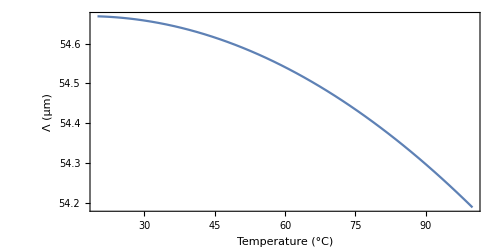

```mathematica
(* Plot the corresponding poling period *)
Plot[
{-2*Pi/Δktype2[0.655,1.31,1.31,t]},
{t,20,100},
FrameLabel->{"Temperature (°C)","Λ (μm)"},
Frame->True,
AspectRatio->1/2,
ImageSize->{500,300},
FrameStyle->Directive[Black,14]]
```

```mathematica
(* Plot the poling period with cte *)
Plot[
{-2*Pi/Δktype2[0.655,1.31,1.31,t]},
{t,20,100},
FrameLabel->{"Temperature (°C)","Λ (μm)"},
Frame->True,
AspectRatio->1/2,
ImageSize->{500,300},
FrameStyle->Directive[Black,14]]
```

-Graphics-